## N = 10000, ϵ = 10^-6, Jacobi_count = 88, Seidel_count = 46, k = N

```mathematica
JacobySendPlusRecv = {{8,79.6869/10.7186},{16,79.6869/5.71773},{24,79.6869/3.97854},{32,79.6869/3.18719},{40,79.6869/3.03466},{48,79.6869/2.605}};
SeidelSendPlusRecv = {{8,42.8026/5.73197},{16,42.8026/3.06325},{24,42.8026/2.14954},{32,42.8026/1.75437},{40,42.8026/1.71375},{48,42.8026/1.52536}};
JacobySendRecv = {{8,79.4485/10.718},{16,79.4485/5.7351},{24,79.4485/4.00091},{32,79.4485/3.17663},{40,79.4485/3.0073},{48,79.4485/2.56883}};
SeidelSendRecv = {{8,43.0041/5.77991},{16,43.0041/3.08524},{24,43.0041/2.17052},{32,43.0041/1.76173},{40,43.0041/1.70456},{48,43.0041/1.53768}};
JacobyISendPlusIRecv = {{8,78.2295/10.5831},{16,78.2295/5.61808},{24,78.2295/3.91411},{32,78.2295/3.11041},{40,78.2295/2.94187},{48,78.2295/2.5277}};
SeidelISendPlusIRecv = {{8,42.0955/5.64168},{16,42.0955/3.02649},{24,42.0955/2.11991},{32,42.0955/1.71978},{40,42.0955/1.65509},{48,42.0955/1.50603}};
```

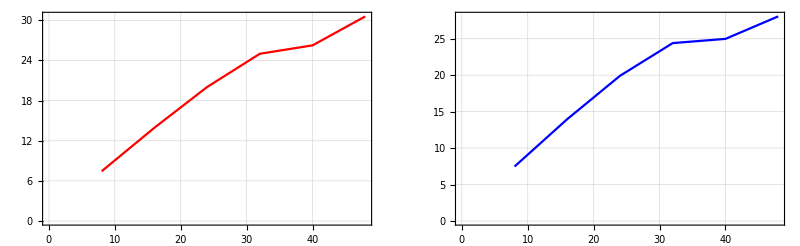

```mathematica
pJacobySendPlusRecv= ListLinePlot[JacobySendPlusRecv,PlotStyle->Red,PlotTheme->"Detailed"];
pSeidelSendPlusRecv= ListLinePlot[SeidelSendPlusRecv,PlotStyle->Blue,PlotTheme->"Detailed"];
GraphicsRow[{pJacobySendPlusRecv,pSeidelSendPlusRecv}]
```

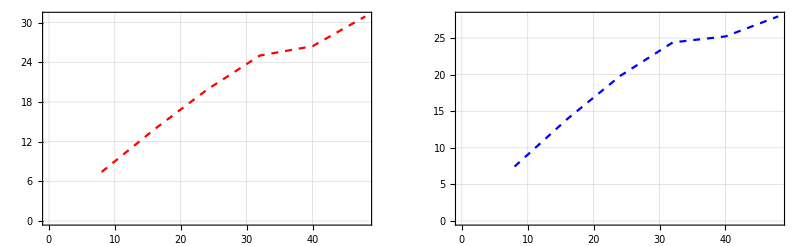

```mathematica
pJacobySendRecv= ListLinePlot[JacobySendRecv,PlotStyle->{Red,Dashed},PlotTheme->"Detailed"];
pSeidelSendRecv= ListLinePlot[SeidelSendRecv,PlotStyle->{Blue,Dashed},PlotTheme->"Detailed"];
GraphicsRow[{pJacobySendRecv,pSeidelSendRecv}]
```

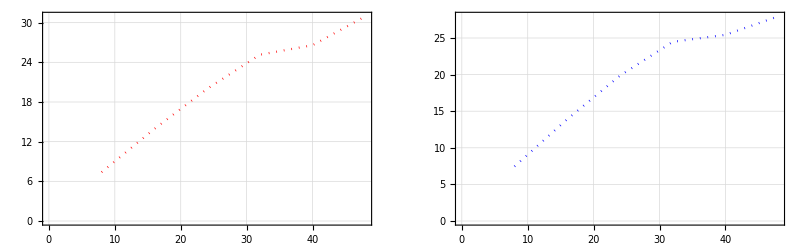

```mathematica
pJacobiISendPlusIRecv= ListLinePlot[JacobyISendPlusIRecv,PlotStyle->{Red,Dotted},PlotTheme->"Detailed"];
pSeidelISendPlusIRecv= ListLinePlot[SeidelISendPlusIRecv,PlotStyle->{Blue,Dotted},PlotTheme->"Detailed"];
GraphicsRow[{pJacobiISendPlusIRecv,pSeidelISendPlusIRecv}]
```

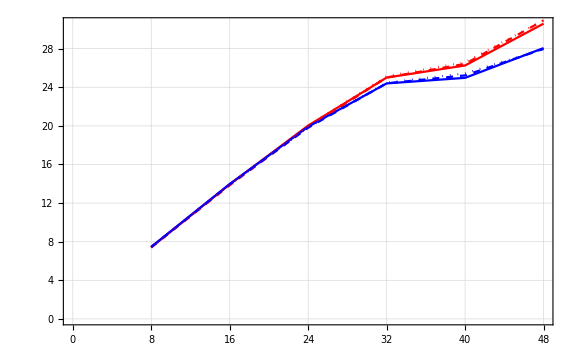

```mathematica
Show[pJacobySendPlusRecv,pSeidelSendPlusRecv,pJacobySendRecv,pSeidelSendRecv,pJacobiISendPlusIRecv,pSeidelISendPlusIRecv,ImageSize->Large]
```

## Контроль над ядрами, N = 10000, ϵ = 10^-6, Jacobi_count = 88, Seidel_count = 46, k = N

```mathematica
JacobySendPlusRecv = {{8,79.6869/11.6095},{16,79.6869/7.53887},{24,79.6869/4.37141},{32,79.6869/3.82609},{40,79.6869/2.69671},{48,79.6869/2.63431},{56,79.6869/2.23202},{64,79.6869/2.0869}};
SeidelSendPlusRecv = {{8,42.8026/6.2188},{16,42.8026/4.32728},{24,42.8026/2.38736},{32,42.8026/2.19745},{40,42.8026/1.61021},{48,42.8026/1.50916},{56,42.8026/1.21944},{64,42.8026/1.17145}};
JacobySendRecv = {{8,79.4485/11.5985},{16,79.4485/7.54669},{24,79.4485/4.30573},{32,79.4485/3.73598},{40,79.4485/2.60281},{48,79.4485/2.54508},{56,79.4485/2.17651},{64,79.4485/1.95563}};
SeidelSendRecv = {{8,43.0041/6.24479},{16,43.0041/4.42731},{24,43.0041/2.39123},{32,43.0041/2.2118},{40,43.0041/1.62544},{48,43.0041/1.51072},{56,43.0041/1.23039},{64,43.0041/1.17462}};
JacobyISendPlusIRecv = {{8,78.2295/11.4708},{16,78.2295/7.46369},{24,78.2295/4.24003},{32,78.2295/3.68373},{40,78.2295/2.52087},{48,78.2295/2.47805},{56,78.2295/2.08075},{64,78.2295/1.86666}};
SeidelISendPlusIRecv = {{8,42.0955/6.16204},{16,42.0955/4.32299},{24,42.0955/2.35517},{32,42.0955/2.17179},{40,42.0955/1.57337},{48,42.0955/1.46854},{56,42.0955/1.17546},{64,42.0955/1.11597}};
```

### Send+Recv

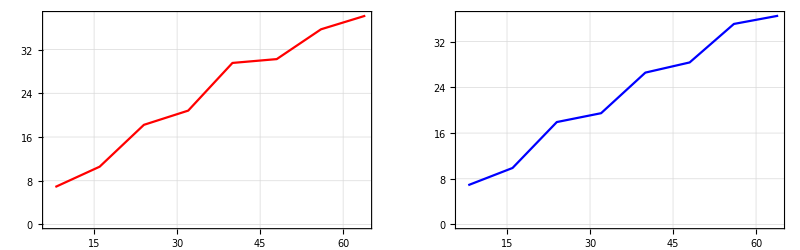

```mathematica
pJacobySendPlusRecv= ListLinePlot[JacobySendPlusRecv,PlotStyle->Red,PlotTheme->"Detailed",PlotRange->All];
pSeidelSendPlusRecv= ListLinePlot[SeidelSendPlusRecv,PlotStyle->Blue,PlotTheme->"Detailed",PlotRange->All];
GraphicsRow[{pJacobySendPlusRecv,pSeidelSendPlusRecv}]
```

### SendRecv

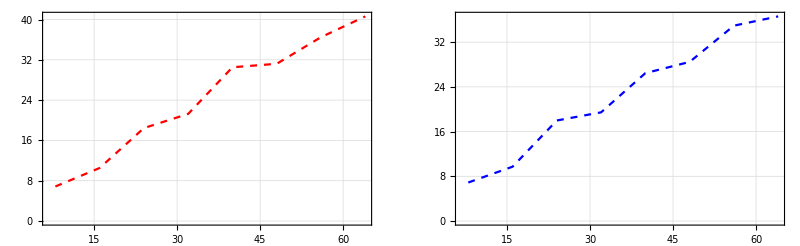

```mathematica
pJacobySendRecv= ListLinePlot[JacobySendRecv,PlotStyle->{Red,Dashed},PlotTheme->"Detailed",PlotRange->All];
pSeidelSendRecv= ListLinePlot[SeidelSendRecv,PlotStyle->{Blue,Dashed},PlotTheme->"Detailed",PlotRange->All];
GraphicsRow[{pJacobySendRecv,pSeidelSendRecv}]
```

### Isend + Irecv

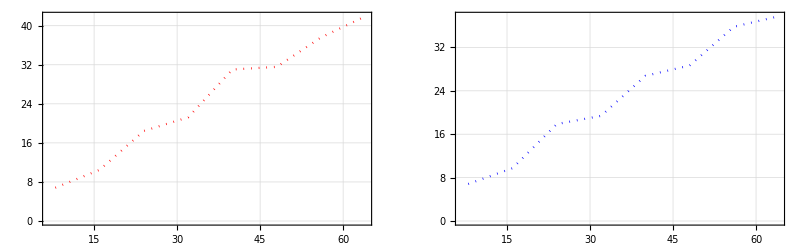

```mathematica
pJacobiISendPlusIRecv= ListLinePlot[JacobyISendPlusIRecv,PlotStyle->{Red,Dotted},PlotTheme->"Detailed",PlotRange->All];
pSeidelISendPlusIRecv= ListLinePlot[SeidelISendPlusIRecv,PlotStyle->{Blue,Dotted},PlotTheme->"Detailed",PlotRange->All];
GraphicsRow[{pJacobiISendPlusIRecv,pSeidelISendPlusIRecv}]
```

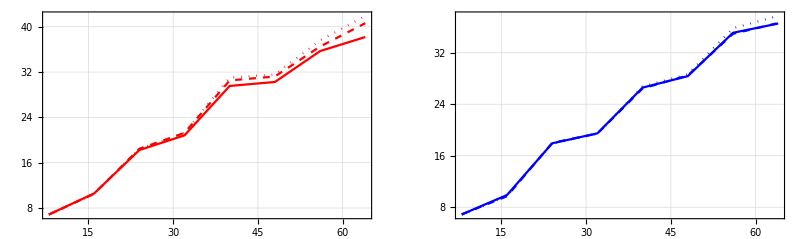

```mathematica
GraphicsRow[{Show[pJacobySendPlusRecv,pJacobySendRecv,pJacobiISendPlusIRecv,ImageSize->Large,PlotRange->All],Show[pSeidelSendPlusRecv,pSeidelSendRecv,pSeidelISendPlusIRecv,ImageSize->Large,PlotRange->All]},ImageSize->Full]
```

## Контроль над ядрами, N = 20000, ϵ = 10^-6, Jacobi_count = 91, Seidel_count = 48, k = N

```mathematica
JacobySendPlusRecv = {{8,333.59/48.1612},{16,333.59/31.2086},{24,333.59/18.0643},{32,333.59/15.6342},{40,333.59/10.5067},{48,333.59/10.3872},{56,333.59/8.53675},{64,333.59/8.08492}};
SeidelSendPlusRecv = {{8,180.64/26.2224},{16,180.64/18.5349},{24,180.64/10.1881},{32,180.64/9.35816},{40,180.64/6.66265},{48,180.64/6.31778},{56,180.64/4.91258},{64,180.64/4.8361}};
JacobySendRecv = {{8,333.474/48.2279},{16,333.474/31.3552},{24,333.474/18.0862},{32,333.474/15.633},{40,333.474/11.4755},{48,333.474/10.6475},{56,333.474/8.44036},{64,333.474/8.02165}};
SeidelSendRecv = {{8,180.956/26.2402},{16,180.956/18.6491},{24,180.956/10.1443},{32,180.956/9.31201},{40,180.956/6.90849},{48,180.956/6.10447},{56,180.956/4.99692},{64,180.956/4.84907}};
JacobyISendPlusIRecv = {{8,325.995/47.6769},{16,325.995/31.23},{24,325.995/17.8589},{32,325.995/15.5115},{40,325.995/11.14},{48,325.995/10.4209},{56,325.995/8.2939},{64,325.995/7.80951}};
SeidelISendPlusIRecv = {{8,177.101/25.899},{16,177.101/18.5056},{24,177.101/10.0149},{32,177.101/9.19362},{40,177.101/6.65067},{48,177.101/6.225},{56,177.101/4.77386},{64,177.101/4.70178}};
```

### Send+Recv

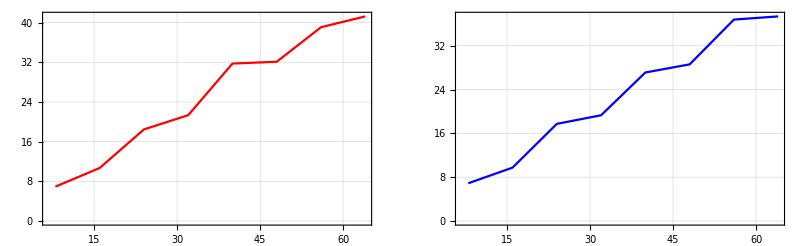

```mathematica
pJacobySendPlusRecv= ListLinePlot[JacobySendPlusRecv,PlotStyle->Red,PlotTheme->"Detailed",PlotRange->All];
pSeidelSendPlusRecv= ListLinePlot[SeidelSendPlusRecv,PlotStyle->Blue,PlotTheme->"Detailed",PlotRange->All];
GraphicsRow[{pJacobySendPlusRecv,pSeidelSendPlusRecv}]
```

### SendRecv

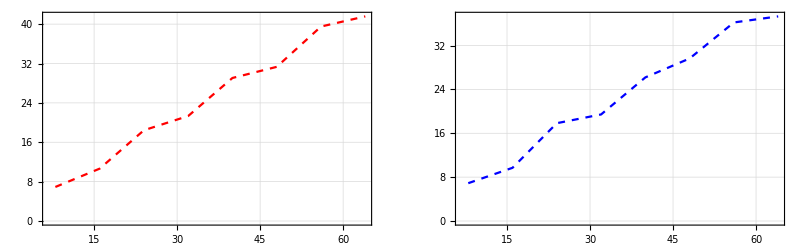

```mathematica
pJacobySendRecv= ListLinePlot[JacobySendRecv,PlotStyle->{Red,Dashed},PlotTheme->"Detailed",PlotRange->All];
pSeidelSendRecv= ListLinePlot[SeidelSendRecv,PlotStyle->{Blue,Dashed},PlotTheme->"Detailed",PlotRange->All];
GraphicsRow[{pJacobySendRecv,pSeidelSendRecv}]
```

### Isend + Irecv

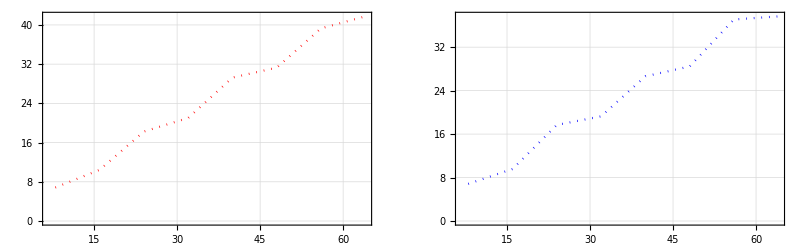

```mathematica
pJacobiISendPlusIRecv= ListLinePlot[JacobyISendPlusIRecv,PlotStyle->{Red,Dotted},PlotTheme->"Detailed",PlotRange->All];
pSeidelISendPlusIRecv= ListLinePlot[SeidelISendPlusIRecv,PlotStyle->{Blue,Dotted},PlotTheme->"Detailed",PlotRange->All];
GraphicsRow[{pJacobiISendPlusIRecv,pSeidelISendPlusIRecv}]
```

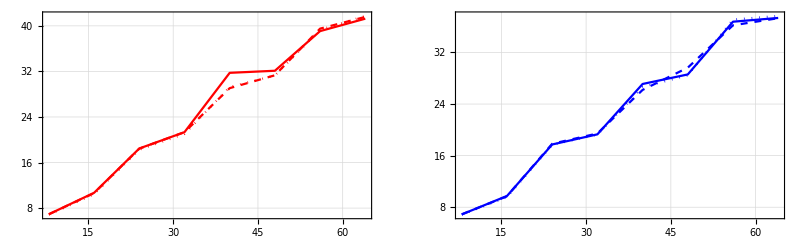

```mathematica
GraphicsRow[{Show[pJacobySendPlusRecv,pJacobySendRecv,pJacobiISendPlusIRecv,ImageSize->Large,PlotRange->All],Show[pSeidelSendPlusRecv,pSeidelSendRecv,pSeidelISendPlusIRecv,ImageSize->Large,PlotRange->All]},ImageSize->Full]
```